# FitzHugh-Nagumo model for single cell

#### Constant stimulation

```mathematica
constStimulation[a_, γ_, ϵ_, Iext_, p_, tmin_, tmax_,minV_, maxV_, minw_, maxw_]:=Module[{eqV, eqw, eql, jacob, eig, sys, vars, init, solution, 
timePlot, nullClines, vectorField, phasePlot, eqlPlot, aPlot, graphs},
eqV[V_,w_]:=1/ϵ*(-w + V*(1-V)*(V-a) + Iext);
eqw[V_,w_]:=V-γ*w;
eql = NSolve[{eqV[V, w] == 0.0, eqw[V, w] == 0.0}, {V, w}, Reals];
jacob = D[{eqV[V, w], eqw[V, w]}, {{V, w}}];
eig = Eigenvalues[jacob/.eql[[1]]];

sys = {D[V[t], t] == eqV[V[t], w[t]], D[w[t], t] == eqw[V[t], w[t]]};
vars = {V[t], w[t]};
init = Thread[{V[tmin], w[tmin]} == p ];
solution = NDSolve[{sys, init}, vars, {t, tmin, tmax}];

timePlot = Plot[Evaluate[vars /. solution], {t, tmin, tmax}, PlotRange->{{tmin, tmax},{minV, maxV}},
			PlotStyle ->{Darker[Red],Gray},Frame -> True, FrameLabel -> {"t", "V, w"}, ImageSize->Large];

(* draw null clines *)
nullClines = ContourPlot[{eqV[V, w]== 0, eqw[V, w]== 0}, {V, minV, maxV}, {w, minw, maxw},
 Frame -> True, FrameLabel -> {"V", "w"}, AspectRatio -> 1, ContourStyle -> {Orange, Darker[Green]}];
 (* draw vector field *)
vectorField = VectorPlot[{eqV[V, w], eqw[V, w] } , {V, minV, maxV}, {w,minw, maxw}, VectorStyle -> {Gray,"PinDart"}, VectorColorFunction->None, VectorPoints -> Fine];
phasePlot = ParametricPlot[Evaluate[vars/.solution], {t, tmin, tmax}, PlotStyle->Darker[Blue]];
(*equilibrium point*)
eqlPlot = ListPlot[{V, w} /. eql, PlotStyle -> {{Black, PointSize[0.02]}}, Frame -> True, FrameLabel -> {"V", "w"}, AspectRatio -> 1];
(*threshold*)
aPlot = ListLinePlot[{{a, minw}, {a, maxw}}];

graphs = GraphicsRow[{Show[nullClines, vectorField, phasePlot, eqlPlot, aPlot], 
			timePlot}, ImageSize->Full];
Column[{Row[{"Real equilibrium at ", eql}], 
Row["with corresponding eigenvalues: ", eig],
graphs}]
]

Manipulate[constStimulation[a, γ, ϵ, Iext, p,tmin, tmax, Vmin, Vmax, wmin,wmax ], 
Style["Model parameters",12],
{{a,0.2,"a"},0.0,1,.01,Appearance-> "Labeled"},
{{γ,0.4,"γ"},0.0,1,.01,Appearance-> "Labeled"},
{{ϵ,0.001,"ϵ"},0.001,1,.01, Appearance-> "Labeled"},
{{Iext,0.0,Subscript[Style["I",Italic],"stim"]},0.0,2,.01, Appearance-> "Labeled"},
Delimiter,
Style["Initial conditions",12],
{{p,{0.0,0.0},Style["p",Italic]},{-1,-1},{1,1}},
Delimiter,
Style[Row[{Style["t",Italic],", ",Style["V",Italic]," and ",Style["w",Italic]," ranges"}],12],
{{tmin,0.0,Subscript[Style["t",Italic],"min"]},0,1000,1, Appearance-> "Labeled"},
{{tmax,1.0,Subscript[Style["t",Italic],"max"]},0,1000,1, Appearance-> "Labeled"},
{{Vmin,-0.5,Subscript[Style["V",Italic],"min"]},-1,1,.01, Appearance-> "Labeled"},
{{Vmax,1.5,Subscript[Style["V",Italic],"max"]},-1,3,.01, Appearance-> "Labeled"},
{{wmin,-0.5,Subscript[Style["w",Italic],"min"]},-1,1,.01, Appearance-> "Labeled"},
{{wmax,1.5,Subscript[Style["w",Italic],"max"]},-1,3,.01, Appearance-> "Labeled"}
]
```

#### Periodic stimulation

```mathematica
periodicStimulation[a_, γ_, ϵ_, tmin_, tmax_, freq_, duration_, strength_]:=Module[{ eqV, eqw, stimuliTrain, S,
sys, vars, init, solution,
plotVw, plotPhase, plotIext,
sol, restTime, rt, drt, apds, poincare},
eqV[V_,w_,Iext_]:=1/ϵ*(-w + V*(1-V)*(V-a) + Iext);
eqw[V_,w_]:=V-γ*w;

stimuliTrain[t_, A_,duty_, T_]:=A*UnitBox[Mod[t/T,1.]/(2. duty)];
S=stimuliTrain[t-(duration+1/2), strength, duration, 1/freq];

sys = {D[V[t], t] == eqV[V[t], w[t],S], D[w[t], t] == eqw[V[t], w[t]]};
vars = {V[t], w[t]};
init = Thread[{V[0], w[0]} =={0.0, 0.0}];
solution = NDSolve[{sys, init}, {V,w}, {t,tmin, tmax}];

plotVw =Plot[Evaluate[{V[t],w[t]}/.solution],{t,tmin,tmax}, PlotStyle->{Darker[Red], Gray},
Frame->True, FrameLabel -> {"t", "V, w"},PlotRange->All];
plotPhase = ParametricPlot[Evaluate[{V[t],w[t]}/.solution],{t,tmin,tmax},
Frame->True, FrameLabel -> {"V", "w"},PlotRange->All];
plotIext = Plot[S,{t,tmin,tmax},PlotStyle->Darker[Green],ExclusionsStyle->Darker[Green],
PlotRange->{All,{0, strength+0.01}},
 Frame->True,FrameLabel -> {"t", "Stimulation"},PlotRange->All];

{sol, restTime} = Reap[
NDSolve[
{sys, init, WhenEvent[V[t]==0, Sow[t]]}, 
{V,w}, {t,tmin, tmax}
]
];
rt = restTime[[1, 2;;]];
drt = Differences[rt];
apds = Pick[drt,Table[Mod[i,2],{i,1,Length@drt}],1];
poincare = ListPlot[
Table[{apds[[i]], apds[[i+1]]}, {i, 1, Length@apds-1}],
PlotStyle->{Orange, PointSize->0.02},
Frame->True, FrameLabel -> {Subscript["APD", "N"], Subscript["APD", "N+1"]},
PlotRange->{{-0.1,0.2}, {-0.1,0.2}}];

 Column[{
GraphicsRow[{Show[plotVw, ImageSize->{500,300}], Show[plotPhase, ImageSize->Medium, AspectRatio->1]}, Spacings->20, ImageSize->Full],
GraphicsRow[{Show[ plotIext, ImageSize->{500,300}], Show[poincare, ImageSize->Medium]}, Spacings->20, ImageSize->Full]
}]
]
```

```mathematica
Manipulate[periodicStimulation[a, γ, ϵ, tmin, tmax,freq,duration,strength], 
Style["Model parameters",12],
{{a,0.2,"a"},0.0,1,.01,Appearance-> "Labeled"},
{{γ,0.4,"γ"},0.0,1,.01,Appearance-> "Labeled"},
{{ϵ,0.001,"ϵ"},0.001,1,.01, Appearance-> "Labeled"},
Delimiter,
{{tmin,0.0,Subscript[Style["t",Italic],"min"]},0,1000,1, Appearance-> "Labeled"},
{{tmax,5.0,Subscript[Style["t",Italic],"max"]},0,1000,1, Appearance-> "Labeled"},
Delimiter,
Style["Stimulation",12],
{{freq,1,"frequency"},0,10,0.01, Appearance-> "Labeled"},
{{duration,0.01,"duration"},0,1,0.01, Appearance-> "Labeled"},
{{strength,0.3,"strength"},0,2,0.01, Appearance-> "Labeled"}]
```

### Periodic stimulation - bifurcation analysis

```mathematica
Quit[]
```

```mathematica
{freqs, APDs}=Reap[Do[
a=0.2; γ=0.4; ϵ=0.001; duration=0.01; strength=0.3; tmin=0; tmax=5;
eqV[V_,w_,Iext_]:=1/ϵ*(-w + V*(1-V)*(V-a) + Iext);
eqw[V_,w_]:=V-γ*w;
stimuliTrain[t_, A_,duty_, T_]:=A*UnitBox[Mod[t/T,1.]/(2. duty)];

vars = {V[t], w[t]};
init = Thread[{V[0], w[0]} =={0.0, 0.0}];
S=stimuliTrain[t-(duration+1/2), strength, duration, 1/f];
sys = {D[V[t], t] == eqV[V[t], w[t],S], D[w[t], t] == eqw[V[t], w[t]]};

restTime={};
NDSolve[
{sys, init, WhenEvent[V[t]==0, AppendTo[restTime,t]]}, 
{V,w}, {t,tmin, tmax}
];
rt = restTime[[2;;]];
drt = Differences[rt];
a = Pick[drt,Table[Mod[i,2],{i,1,Length@drt}],1];
Sow[f, freq];
Sow[a, apds],
{f, 0.1, 15, 0.1}
]][[2]];
```

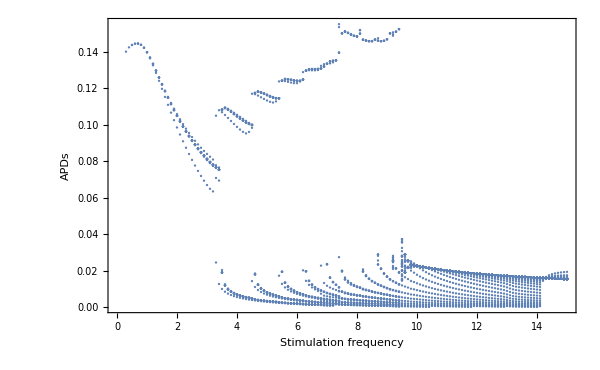

```mathematica
pts=Reap[
Do[
Sow[{freqs[[i]], APDs[[i, j]]}, p],
{i, 1, Length@freqs}, {j, 1, Length@APDs[[i]]}]
][[2,1]];
ListPlot[pts, PlotRange->All,
Frame->True, FrameLabel->{Style["Stimulation frequency", FontSize->12], Style["APDs", FontSize->12]}, ImageSize->{600,400}]
```

```mathematica
x=2.5234
If[FractionalPart[x]<0.5, Floor[x], Ceiling[x]]
```

2.5234

```mathematica
{freqs, APDs}=Reap[Do[
a=0.2; γ=0.4; ϵ=0.001; duration=0.01; strength=0.3; tmin=0; tmax=5;
eqV[V_,w_,Iext_]:=1/ϵ*(-w + V*(1-V)*(V-a) + Iext);
eqw[V_,w_]:=V-γ*w;
stimuliTrain[t_, A_,duty_, T_]:=A*UnitBox[Mod[t/T,1.]/(2. duty)];

vars = {V[t], w[t]};
init = Thread[{V[0], w[0]} =={0.0, 0.0}];
S=stimuliTrain[t-(duration+1/2), strength, duration, 1/f];
sys = {D[V[t], t] == eqV[V[t], w[t],S], D[w[t], t] == eqw[V[t], w[t]]};

restTime={};
NDSolve[
{sys, init, WhenEvent[V[t]==0, AppendTo[restTime,t]]}, 
{V,w}, {t,tmin, tmax}
];
rt = restTime[[2;;]];
drt = Differences[rt];
a = Pick[drt,Table[Mod[i,2],{i,1,Length@drt}],1];
Sow[f, freq];
Sow[a, apds],
{f, 0.1, 15, 0.1}
]][[2]];
```